```mathematica
(* This Mathematica notebook computes the Berry curvature for a specific toy model *)
k = {kx,ky};
```

```mathematica
(*Fix the honeycomb lattice constant to unity so all lengths are measured in units of a*)
a = 1;
```

```mathematica
(*The three nearest-neighbour bond vectors linking the A and B sublattices of the honeycomb*)
a1 = {0,a};a2 = {-(√3/2)a, -a/2};a3 = {(√3/2)a, -a/2};
```

```mathematica
(*First next-nearest-neighbour vector, a primitive translation of the underlying triangular Bravais lattice*)
b1 = a2 - a3;
```

```mathematica
(*Second next-nearest-neighbour vector*)
b2 = a3 - a1;
```

```mathematica
(*Third next-nearest-neighbour vector*)
b3 = a1 - a2;
```

```mathematica
(*Two by two identity matrix, the sublattice-independent part of the Hamiltonian*)
σ0 = PauliMatrix[0];
```

```mathematica
(*Pauli matrix sigma_x acting in the A-B sublattice pseudospin space*)
σ1 = PauliMatrix[1];
```

```mathematica
(*Pauli matrix sigma_y in sublattice space*)
σ2 = PauliMatrix[2];
```

```mathematica
(*Pauli matrix sigma_z in sublattice space*)
σ3 = PauliMatrix[3];
```

```mathematica
(*Sublattice-independent energy from next-nearest-neighbour hopping; it shifts both bands equally and leaves the eigenvectors unchanged*)
ϵ = 2*t2*Cos[ϕ]*(Cos[k.b1]+ Cos[k.b2]+ Cos[k.b3]);
```

```mathematica
(*Real part of the nearest-neighbour hopping, the coefficient multiplying sigma_x*)
dx = t1*(Cos[k.a1]+ Cos[k.a2]+ Cos[k.a3]);
```

```mathematica
(*Imaginary part of the nearest-neighbour hopping, the coefficient multiplying sigma_y*)
dy = t1*(Sin[k.a1]+Sin[k.a2]+Sin[k.a3]);
```

```mathematica
(*Sublattice mass M minus the Haldane next-nearest-neighbour flux term; this is the coefficient of sigma_z that can invert the band gap*)
dz = M - 2*t2*Sin[ϕ]* (Sin[k.b1] + Sin[k.b2]+Sin[k.b3]);
```

```mathematica
(*Assemble the two-band Bloch Hamiltonian H(k) as epsilon times the identity plus the vector d dotted into the Pauli matrices*)
H = ϵ*σ0 + dx*σ1 + dy*σ2+dz*σ3;
```

```mathematica
Hamiltonian[M0_,t10_,t20_,ϕ0_,kx0_,ky0_]:=H/.{M->M0,t1->t10,t2->t20,ϕ->ϕ0,kx->kx0,ky->ky0} (* This builds the k dot p Hamiltonian for us *)
```

```mathematica
(*Numerically evaluate H at one sample momentum, displayed in traditional form, to confirm it returns a Hermitian matrix*)
Hamiltonian[0.1,10,0.2,0.2*π,1,1]//N//TraditionalForm
```

(0.284429 | 16.774-2.2027 ⅈ
16.774+2.2027 ⅈ | -0.329023)

```mathematica
(*Redefine the parametrised Hamiltonian, identical to the definition given above*)
Hamiltonian[M0_,t10_,t20_,ϕ0_,kx0_,ky0_]:=H/.{M->M0,t1->t10,t2->t20,ϕ->ϕ0,kx->kx0,ky->ky0};
```

```mathematica
num = 100; (* this is the number of grid points we need to divide kx and ky into *)
```

```mathematica
{A1,B1} = {-π,π}; (* this is the extent of kx *)
```

```mathematica
{A2,B2} = {-π,π}; (* this is the extent of ky *)
```

```mathematica
(*Spacing of the kx grid: the kx range divided into num intervals*)
deltakx = (B1 - A1)/100;
```

```mathematica
(*Spacing of the ky grid*)
deltaky = (B2 - A2)/100;
```

```mathematica
(*The kx sample points, running from the left edge up to one step short of the right edge so the grid tiles the patch without repetition*)
kxPoints = Table[kx,{kx,A1,B1-deltakx,deltakx}]//N;
```

```mathematica
(*The ky sample points, built the same way*)
kyPoints = Table[ky,{ky,A2,B2-deltaky,deltaky}]//N;
```

```mathematica
(*Diagonalise H on the base grid; Transpose pairs each eigenvalue with its eigenvector and Sort orders the pairs by ascending energy so the lower occupied band comes first*)
eigensystem =Table[Transpose[Eigensystem[Hamiltonian[0.1,10,0.2,0.2*π,kxPoints[[i]],kyPoints[[j]]]//N//Chop]]//Sort,{i,1,num},{j,1,num}]
```

{{{{-20.6003,{-0.337471+0.616035 ⅈ,-0.711768+0. ⅈ}},{21.0315,{0.341965-0.624239 ⅈ,1}}},98,1},98,{1}}
 |  |  |  |

```mathematica
(*Inspect the two sorted energy-eigenvector pairs at the first grid point*)
eigensystem[[1,1]]
```

{{-20.6003,{-0.337471+0.616035 ⅈ,-0.711768+0. ⅈ}},{21.0315,{0.341965-0.624239 ⅈ,-0.702414+0. ⅈ}}}

```mathematica
(*The lower-band pair, its energy together with its eigenvector, at that point*)
eigensystem[[1,1,1]]
```

{-20.6003,{-0.337471+0.616035 ⅈ,-0.711768+0. ⅈ}}

```mathematica
(*The lower-band eigenvector on its own*)
eigensystem[[1,1,1,2]]
```

{-0.337471+0.616035 ⅈ,-0.711768+0. ⅈ}

```mathematica
(*Act with H on a lower-band eigenvector, a check that it returns energy times the vector*)
Hamiltonian[0.1,10,0.2,0.2*π,kxPoints[[1]],kyPoints[[2]]].eigensystem[[1,2,1,2]]
```

{7.32554-13.1005 ⅈ,15.1892-3.55271×10^-15 ⅈ}

```mathematica
(*Energy multiplied by the same eigenvector, for comparison with the previous line*)
eigensystem[[1,2,1,1]]*eigensystem[[1,2,1,2]]
```

{7.32554-13.1005 ⅈ,15.1892+0. ⅈ}

```mathematica
(*Allocate a num by num table to hold the lower-band kets*)
Array[vecket,{num,num}];
```

```mathematica
(*Store the lower-band eigenvector at each grid point as a column vector, the ket*)
Table[vecket[i,j]= Transpose[{eigensystem[[i,j,1,2]]}],{i,1,num},{j,1,num}];
```

```mathematica
(*Allocate storage for the matching bras*)
Array[vecbra,{num,num}];
```

```mathematica
(*Each bra is the conjugate transpose of the ket at that grid point*)
Table[vecbra[i,j] =ConjugateTranspose[vecket[i,j]],{i,1,num},{j,1,num}];
```

```mathematica
(*Rediagonalise on the grid shifted by one step in kx, overwriting eigensystem*)
eigensystem=Table[Transpose[Eigensystem[Hamiltonian[0.1,10,0.2,0.2*π,kxPoints[[i]]+deltakx,kyPoints[[j]]]//N//Chop]]//Sort,{i,1,num},{j,1,num}];
```

```mathematica
(*Allocate kets for the kx-shifted grid*)
Array[vecDeltaKxket,{num,num}];
```

```mathematica
(*Store the lower-band kets at momenta shifted by deltakx along x*)
Table[vecDeltaKxket[i,j]=Transpose[{eigensystem[[i,j,1,2]]}],{i,1,num},{j,1,num}];
```

```mathematica
(*Allocate the matching bras*)
Array[vecDeltaKxbra,{num,num}];
```

```mathematica
(*Bras for the kx-shifted grid*)
Table[vecDeltaKxbra[i,j]=ConjugateTranspose[vecDeltaKxket[i,j]],{i,1,num},{j,1,num}];
```

```mathematica
(*Rediagonalise on the grid shifted by one step in ky*)
eigensystem = Table[Transpose[Eigensystem[Hamiltonian[0.1,10,0.2,0.2*π,kxPoints[[i]],kyPoints[[j]]+deltaky]//N//Chop]]//Sort,{i,1,num},{j,1,num}];
```

```mathematica
(*Allocate kets for the ky-shifted grid*)
Array[vecDeltaKyket,{num,num}];
```

```mathematica
(*Store the lower-band kets at momenta shifted by deltaky along y*)
Table[vecDeltaKyket[i,j]=Transpose[{eigensystem[[i,j,1,2]]}],{i,1,num},{j,1,num}];
```

```mathematica
(*Allocate the matching bras*)
Array[vecDeltaKybra,{num,num}];
```

```mathematica
(*Bras for the ky-shifted grid*)
Table[vecDeltaKybra[i,j]=ConjugateTranspose[vecDeltaKyket[i,j]],{i,1,num},{j,1,num}];
```

```mathematica
(*Rediagonalise on the grid shifted by one step in both kx and ky, the far corner of each plaquette*)
eigensystem = Table[Transpose[Eigensystem[Hamiltonian[0.1,10,0.2,0.2*π,kxPoints[[i]]+deltakx,kyPoints[[j]]+ deltaky]//N//Chop]]//Sort,{i,1,num},{j,1,num}];
```

```mathematica
(*Allocate kets for the diagonally shifted grid*)
Array[vecDeltaKxKyket,{num,num}];
```

```mathematica
(*Store the lower-band kets at momenta shifted by both deltakx and deltaky*)
Table[vecDeltaKxKyket[i,j]= Transpose[{eigensystem[[i,j,1,2]]}],{i,1,num},{j,1,num}];
```

```mathematica
(*Allocate the matching bras*)
Array[vecDeltaKxKybra,{num,num}];
```

```mathematica
(*Bras for the diagonally shifted grid*)
Table[vecDeltaKxKybra[i,j]=ConjugateTranspose[vecDeltaKxKyket[i,j]],{i,1,num},{j,1,num}];
```

```mathematica
(* We now define the global U(1) phase link variable *)
Array[Ux,{num,num}];
```

```mathematica
(*Fukui-Hatsugai-Suzuki link variable along kx: the overlap of a ket with its kx neighbour, divided by its modulus to leave a pure U(1) phase*)
Table[Ux[i,j]= (vecbra[i,j].vecDeltaKxket[i,j]/Abs[vecbra[i,j].vecDeltaKxket[i,j]])[[1,1]],{i,1,num},{j,1,num}];
```

```mathematica
(*Allocate the link variables along ky*)
Array[Uy,{num,num}];
```

```mathematica
(*Link variable along ky, the normalised overlap between a ket and its ky neighbour*)
Table[Uy[i,j]=(vecbra[i,j].vecDeltaKyket[i,j]/Abs[vecbra[i,j].vecDeltaKyket[i,j]])[[1,1]],{i,1,num},{j,1,num}];
```

```mathematica
(*Allocate the kx link variables evaluated on the upper edge of each plaquette*)
Array[Uxy,{num,num}];
```

```mathematica
(*Link variable along kx taken on the ky-shifted upper side of the plaquette*)
Table[Uxy[i,j]=(vecDeltaKybra[i,j].vecDeltaKxKyket[i,j]/Abs[vecDeltaKybra[i,j].vecDeltaKxKyket[i,j]])[[1,1]],{i,1,num},{j,1,num}];
```

```mathematica
(*Allocate the ky link variables evaluated on the right edge of each plaquette*)
Array[Uyx,{num,num}];
```

```mathematica
(*Link variable along ky taken on the kx-shifted right side of the plaquette*)
Table[Uyx[i,j]=(vecDeltaKxbra[i,j].vecDeltaKxKyket[i,j]/Abs[vecDeltaKxbra[i,j].vecDeltaKxKyket[i,j]])[[1,1]],{i,1,num},{j,1,num}];
```

```mathematica
(*Allocate the lattice field strength on each plaquette*)
Array[F,{num,num}];
```

```mathematica
(*Lattice Berry field strength on each plaquette: the logarithm of the product of the four link variables around the loop, taken on the principal branch so its imaginary part lies between minus pi and pi*)
Table[F[i,j]= Log[Ux[i,j]*Uyx[i,j]/(Uxy[i,j]*Uy[i,j])],{i,1,num},{j,1,num}];
```

```mathematica
(*Berry curvature at each plaquette: the field strength divided by the plaquette area and multiplied by i to make it real, tabulated as {kx, ky, curvature} for plotting*)
BerryCurvature=Flatten[Table[{kxPoints[[i]],kyPoints[[j]],F[i,j]* I/deltakx/deltaky},{i,1,num},{j,1,num}],1];
```

```mathematica
(*Chern number: sum the field strength over every plaquette in the sampled patch and divide by 2 pi i; for these parameters the plaquette sum evaluates to about 2.99*)
ChernNumber= Total[Flatten[Table[-F[i,j],{i,1,num},{j,1,num}]]]/(2π*I)
```

1.48585+4.14532×10^-14 ⅈ

```mathematica
(*Surface plot of the Berry curvature over the sampled patch of momentum space*)
ListPlot3D[BerryCurvature,PlotRange->Full,PlotLegends->Automatic,ColorFunction->Hue]
```

-Graphics3D-

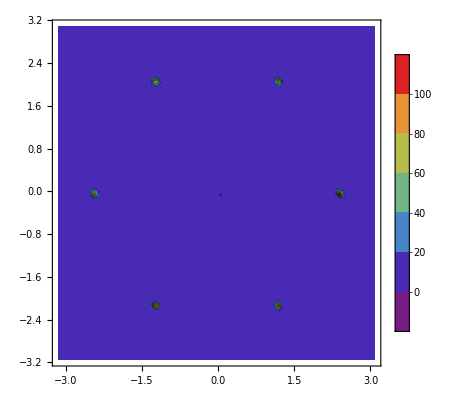

```mathematica
(*Contour plot of the same Berry curvature*)
ListContourPlot[BerryCurvature,PlotRange->Full,PlotLegends->Automatic,ColorFunction->"Rainbow"]
```

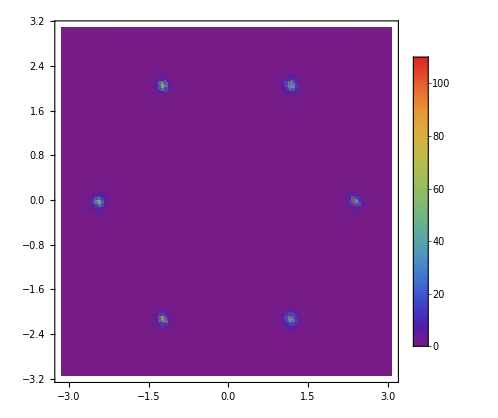

```mathematica
(*Density plot of the same Berry curvature*)
ListDensityPlot[BerryCurvature,PlotLegends->Automatic,PlotRange->Full,ColorFunction->"Rainbow"]
```